```mathematica
pts3=Table[{Cos[2n π/7],Sin[2 n π/7]},{n,0,6}]
```

{{1,0},{Sin[(3 π)/14],Cos[(3 π)/14]},{-Sin[π/14],Cos[π/14]},{-Cos[π/7],Sin[π/7]},{-Cos[π/7],-Sin[π/7]},{-Sin[π/14],-Cos[π/14]},{Sin[(3 π)/14],-Cos[(3 π)/14]}}

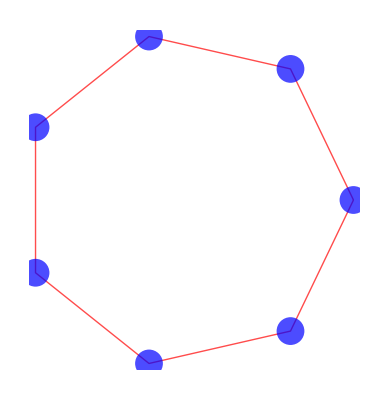

```mathematica
Graphics[{Opacity[0.7],Red,Line[pts3[[Last[FindShortestTour[pts3]]]]],Blue,PointSize[0.05],Point[pts3]}]
```

```mathematica
a=EuclideanDistance[{1,0},{Sin[(3 π)/14],-Cos[(3 π)/14]}];
b=EuclideanDistance[{Sin[(3 π)/14],-Cos[(3 π)/14]},{Sin[(3 π)/14],Cos[(3 π)/14]}];
c=EuclideanDistance[{Sin[(3 π)/14],-Cos[(3 π)/14]},{-Sin[π/14],Cos[π/14]}];
Simplify[b^2/a^2+c^2/b^2+a^2/c^2]
```

5/8 Sec[π/14]^2 Sec[(3 π)/14]^2 (2+2 Cos[π/7]+Sin[π/14]+Sin[(3 π)/14])

```mathematica
N[(5 Sec[(3 π)/14]^2 (2+2 Cos[π/7]+Sin[π/14]+Sin[(3 π)/14]))/(4 (Cos[(5 π)/28]+Sin[(5 π)/28])^2)]
```

5.